```mathematica
SetDirectory["/home/s1220054/Dissertation/Dissertation/DiSamp/src"]
```

/home/s1220054/Dissertation/Dissertation/DiSamp/src

```mathematica
data = Import["phidist.txt","CSV"]
```

{{42.5206,0},{32.2025,0.333333},{55.6058,0.428571},{20,0.428571},{25.807,0.416667},{28.7924,0.428571},{48.7647,0.428571},22677,{53.9073,0.500187},{6,0.500209},{64.8999,0.500209},{84.5931,0.500209},{48.2597,0.500231},{23.7697,0.500231}}
 |  |  |  |

```mathematica
Transpose[data]
```

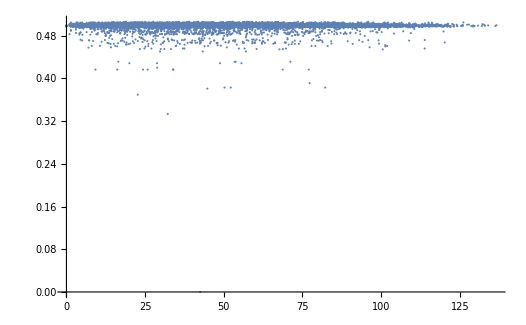

```mathematica
ListPlot[data]
```

```mathematica
data2 = Import["new.txt","CSV"]
```

{{260,294},{260,301},{260,302},{260,303},{260,304},{260,305},{260,306},{260,307},{261,292},{261,293},{261,294},{261,295},{261,296},4012,{337,287},{337,294},{337,296},{337,299},{337,306},{337,308},{337,309},{337,310},{338,281},{338,296},{339,279},{339,281},{340,281}}
 |  |  |  |

```mathematica
data3 = Import["type2.txt","CSV"]
```

{{261,289},{261,290},{261,291},{261,323},{262,288},{262,289},{262,291},{262,292},{262,296},{262,312},{262,321},{262,322},{262,323},3580,{339,286},{339,287},{339,288},{339,289},{339,290},{339,292},{340,280},{340,283},{340,284},{340,285},{340,289},{340,290},{340,291}}
 |  |  |  |

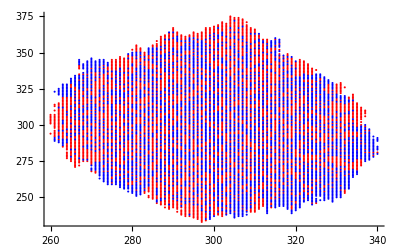

```mathematica
ListPlot[{data2,data3},PlotStyle->{Red,Blue}]
```